```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarF1[m_,s_]:=2-2Log[m]+(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
ScalarFPrime1[m_,s_]:=-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))(ArcTan[(√s)/(√(4 m^2-s))]-π);
PropagatorScalar[s_,M_,m_,c_]:=Abs[1+c×ScalarFPrime1[m,M^2]]/(s-M^2+c×(ScalarF0[m,s]-ScalarF1[m,M^2]));
```

```mathematica
NWA[p_,A_,B_,C_]:=C/((p^2-A)^2+B);
```

```mathematica
BestFit[m_,c_,Γ_]:=NMinimize[{Sum[((Abs[PropagatorScalar[p^2,1-ⅈ×Γ/2,m,c]]^2-NWA[p,A,B,C])^2)/(Abs[PropagatorScalar[p^2,1-ⅈ×Γ/2,m,c]]^2),{p,0.01,2,0.01}],A>0,B>0,C>0},{A,B,C},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->MachinePrecision];
```

```mathematica
Res1=BestFit[0.40001,0.04,0.3]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.4887,{A→0.974422,B→0.0730324,C→0.828043}}

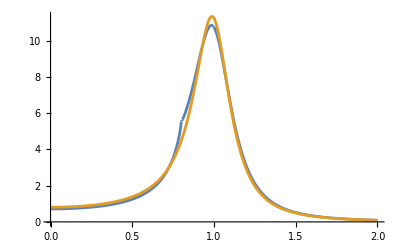

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.40001,0.04]]^2,NWA[p,A,B,C]/.Res1[[2]]},{p,0,2}]
```

```mathematica
Res2=BestFit[0.45001,0.04,0.3]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{3.21068,{A→0.98663,B→0.0631996,C→0.715946}}

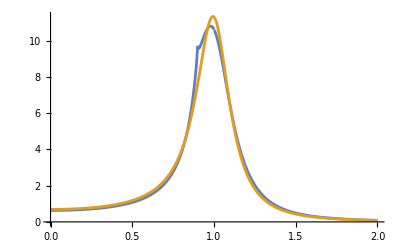

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.45001,0.04]]^2,NWA[p,A,B,C]/.Res2[[2]]},{p,0,2}]
```

```mathematica
Res3=BestFit[0.50001,0.04,0.3]
```

{2.72633,{A→1.01886,B→0.0524983,C→0.596715}}

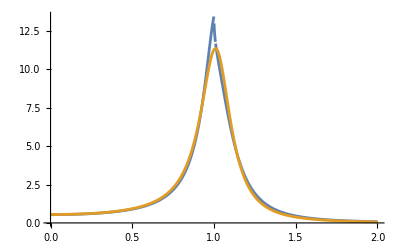

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.50001,0.04]]^2,NWA[p,A,B,C]/.Res3[[2]]},{p,0,2},PlotRange->All]
```

```mathematica
Res4=BestFit[0.55001,0.04,0.3]
```

{1.21044,{A→1.07461,B→0.0485614,C→0.562285}}

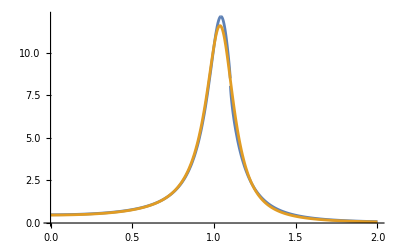

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.55001,0.04]]^2,NWA[p,A,B,C]/.Res4[[2]]},{p,0,2},PlotRange->All]
```

```mathematica
Res5=BestFit[0.60001,0.04,0.3]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.430714,{A→1.12745,B→0.0496535,C→0.580781}}

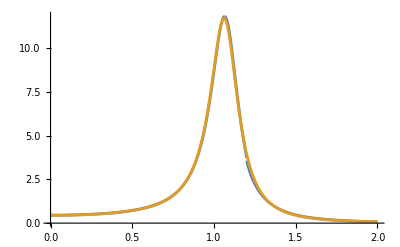

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.60001,0.04]]^2,NWA[p,A,B,C]/.Res5[[2]]},{p,0,2},PlotRange->All]
```

```mathematica
Res6=BestFit[0.45001,0.02,0.15]
```

{2.23966,{A→0.995434,B→0.0197127,C→0.879275}}

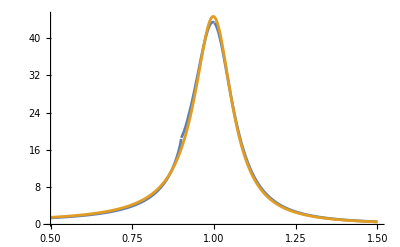

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.15/2,0.45001,0.02]]^2,NWA[p,A,B,C]/.Res6[[2]]},{p,0.5,1.5},PlotRange->All]
```

```mathematica
Res7=BestFit[0.50001,0.02,0.15]
```

{3.15755,{A→1.01029,B→0.0164685,C→0.731524}}

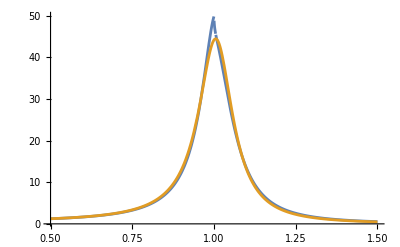

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.15/2,0.50001,0.02]]^2,NWA[p,A,B,C]/.Res7[[2]]},{p,0.5,1.5},PlotRange->All]
```

```mathematica
Res8=BestFit[0.55001,0.02,0.15]
```

{0.749837,{A→1.04723,B→0.0161506,C→0.721618}}

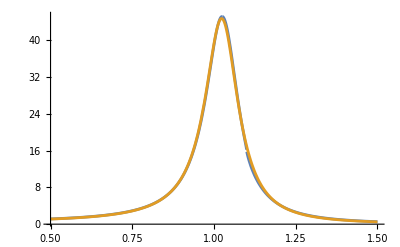

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.15/2,0.55001,0.02]]^2,NWA[p,A,B,C]/.Res8[[2]]},{p,0.5,1.5},PlotRange->All]
```

```mathematica
Res9=BestFit[0.48001,0.02,0.15]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{3.28492,{A→1.0006,B→0.0179317,C→0.797284}}

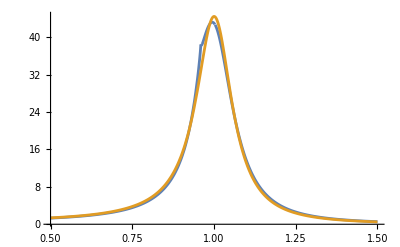

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.15/2,0.48001,0.02]]^2,NWA[p,A,B,C]/.Res9[[2]]},{p,0.5,1.5},PlotRange->All]
```

```mathematica
Res10=BestFit[0.49001,0.008,0.06]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{3.58534,{A→1.0003,B→0.00322586,C→0.898051}}

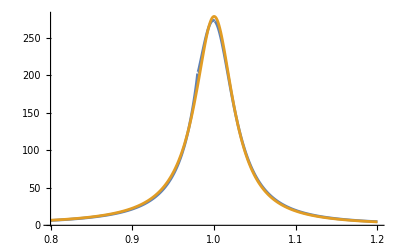

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.06/2,0.49001,0.008]]^2,NWA[p,A,B,C]/.Res10[[2]]},{p,0.8,1.2},PlotRange->All]
```

```mathematica
Res11=BestFit[0.50001,0.008,0.06]
```

{4.07262,{A→1.00325,B→0.00301272,C→0.842259}}

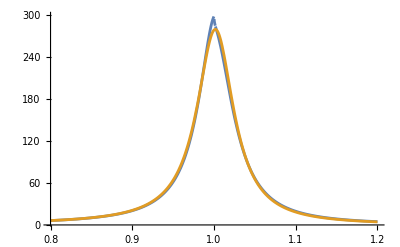

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.06/2,0.50001,0.008]]^2,NWA[p,A,B,C]/.Res11[[2]]},{p,0.8,1.2},PlotRange->All]
```